```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
RedC=RGBColor[0.60,0.30,0];
```

## Choosing heat capacity of the intermediate bath for time domain simulations

The heat capacity of a thermal bath is given by the equation

C_I(T_I)=k_B∑_(k=0)^(Ns-1) ((ℏ ω_k^I)/(k_B T_I))^2(ⅇ^((ℏ ω_k^I)/(k_B T_I)))/((ⅇ^((ℏ ω_k^I)/(k_B T_I))-1)^2)

Here, Ns is the total number of oscillators in the intermediate bath.

Assume that we work in natural units and that the bath oscillators are uniformly distributed from ω_min to ω_max.

```mathematica
unitassum={kB->1,ℏ->1};
oscassum={Subscript[ω, k]->ωmin+(ωmax-ωmin)/(Ns-1)k};
```

Plot the heat capacity graph for a uniformly distributed oscillator set

```mathematica
Manipulate[
Module[{temp},
Cs=kB∑_(k=0)^(Ns-1) ((ℏ Subscript[ω, k])/(kB T))^2 ⅇ^((ℏ Subscript[ω, k])/(kB T))/((ⅇ^((ℏ Subscript[ω, k])/(kB T))-1)^2);
temp=Evaluate[Cs//.Flatten[{Ns->Nss,ωmax->ωmaxs,ωmin->ωmins,unitassum,oscassum}]];
Plot[temp,{T,0.02,0.2},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["k_BT_I/ℏΔ",FontFamily->"Times New Roman",FontSize->16],
Style["C_I/k_B",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}}
]
],
Delimiter,Item["Frequency paramters",Alignment->Center],
{{ωmins,0.1},0.001,1},
{{ωmaxs,0.5},0.001,1},
Delimiter,Item["Number of oscillators",Alignment->Center],
{{Nss,100},10,150,1}]
```

The frequency range [ω_min,ω_max] was specifically chosen to include the transition frequencies of the transistors on either side. 
The number of oscillators was chosen as Ns=100. Generally that number of oscillators are considered for proper alignment with Born and Markov approximations.

Since we are anyway doing only a rough calculation, for simplicity we assume the heat capacity is independent of temperature. 
Therefore for time domain calculations, we choose an average heat capacity of around C=50 k_B for the intermediate bath.

#### Energy capacity of a single oscillator (approximated from its heat capacity)

```mathematica
kB ((ℏ Subscript[ω, k])/(kB T))^2 ⅇ^((ℏ Subscript[ω, k])/(kB T))/((ⅇ^((ℏ Subscript[ω, k])/(kB T))-1)^2)//.Flatten[{Subscript[ω, k]->0.2,T->0.05,unitassum}]
kB ((ℏ Subscript[ω, k])/(kB T))^2 ⅇ^((ℏ Subscript[ω, k])/(kB T))/((ⅇ^((ℏ Subscript[ω, k])/(kB T))-1)^2)//.Flatten[{Subscript[ω, k]->0.2,T->0.20,unitassum}]
```

0.304087

0.920674

## Energy divider (2,1) analysis

## ω_LM^S_1=0.3Δ, ω_MR^S_1=0.4Δ ω_LM^S_2=0.9Δ, ω_MR^S_2=1.1Δ ω_H=0.2Δ

### Temperature controlled

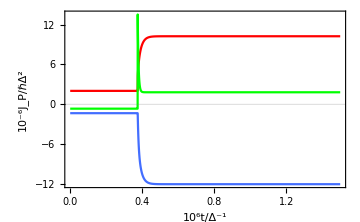
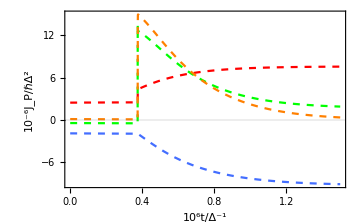
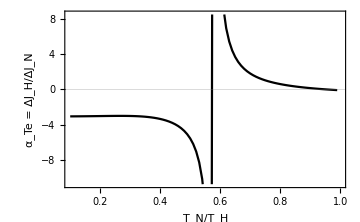
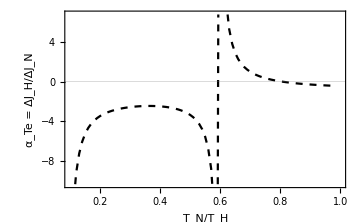
```mathematica
engdiv=-Graphics-;intbath=-Graphics-;
Legended[Show[engdiv,intbath,PlotRange->{-12,16}],LineLegend[{Red,Green,BlueC,Directive[Orange,Dashed]},{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5]}]]
engdiv=-Graphics-;intbath=-Graphics-;
Show[engdiv,intbath,PlotRange->{{0.1,1.0},{-10,6}}]
```

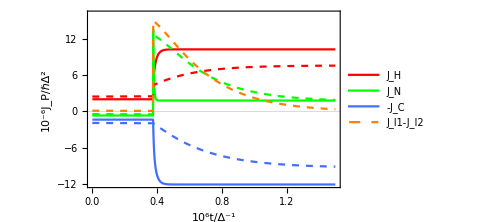

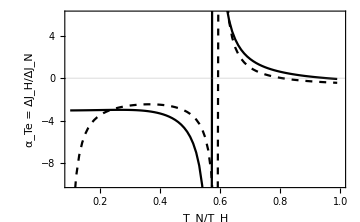

### Optically controlled

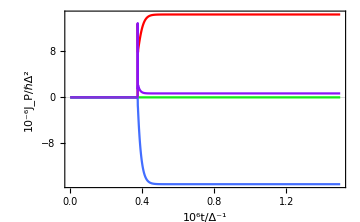
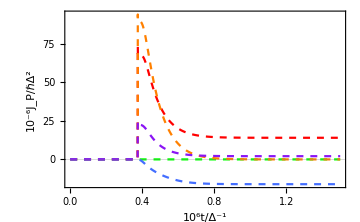
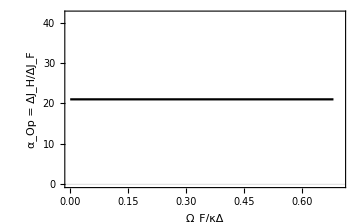
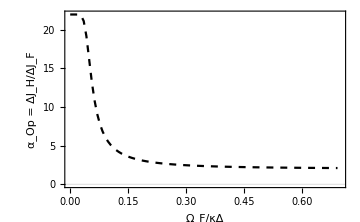
```mathematica
engdiv=-Graphics-;intbath=-Graphics-;
Legended[Show[engdiv,intbath,PlotRange->{-16,30}],LineLegend[{Red,Green,BlueC,PurpleC,Directive[Orange,Dashed]},{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5]}]]
engdiv=-Graphics-;intbath=-Graphics-;
Show[engdiv,intbath,PlotRange->{{0.0,0.7},{-1,25}}]
```

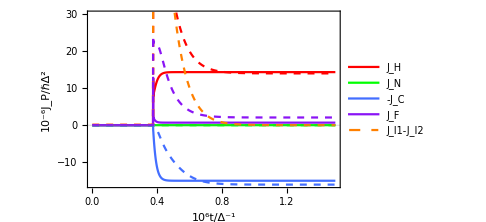

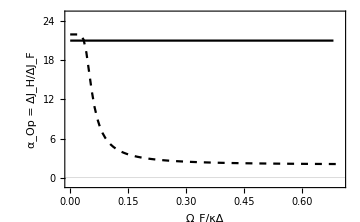

## ω_LM^S_1=0.5Δ, ω_MR^S_1=0.6Δ ω_LM^S_2=0.85Δ, ω_MR^S_2=1.15Δ ω_H=0.3Δ

### Temperature controlled

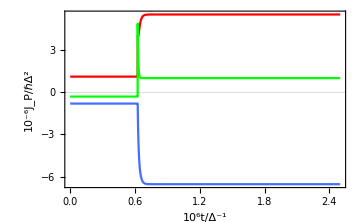
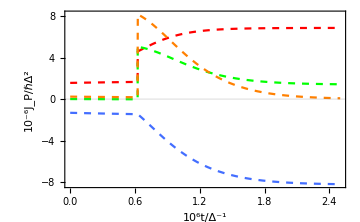
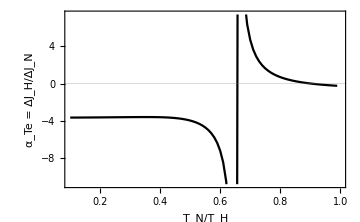
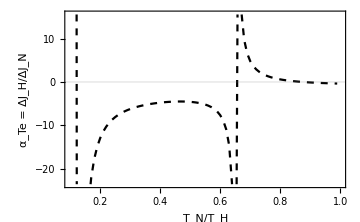
```mathematica
engdiv=-Graphics-;intbath=-Graphics-;
Legended[Show[engdiv,intbath,PlotRange->{-8,8}],LineLegend[{Red,Green,BlueC,Directive[Orange,Dashed]},{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5]}]]
engdiv=-Graphics-;intbath=-Graphics-;
Show[engdiv,intbath]
```

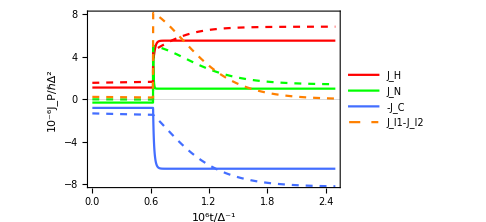

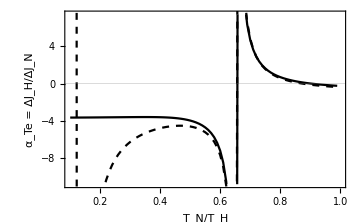

### Optically controlled

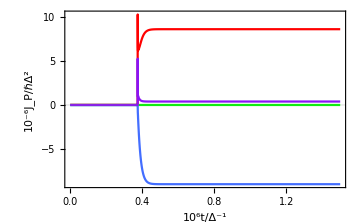
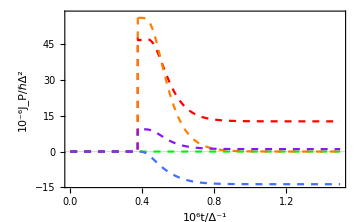
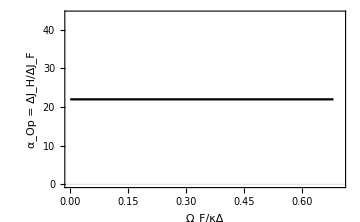
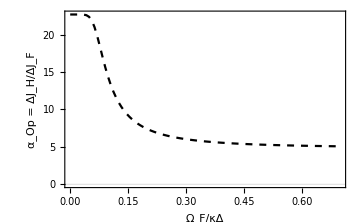
```mathematica
engdiv=-Graphics-;intbath=-Graphics-;
Legended[Show[engdiv,intbath,PlotRange->{-13,25}],LineLegend[{Red,Green,BlueC,PurpleC,Directive[Orange,Dashed]},{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5]}]]
engdiv=-Graphics-;intbath=-Graphics-;
Show[engdiv,intbath]
```

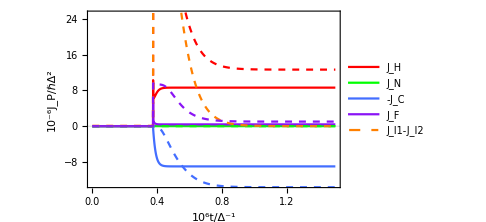

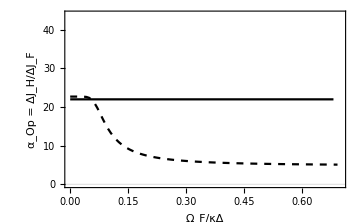

## Energy divider (3,1) analysis

## ω_LM^S_1=0.5Δ, ω_MR^S_1=0.6Δ ω_LM^S_2=0.9Δ, ω_MR^S_2=1.1Δ ω_H=0.2Δ

### Temperature controlled

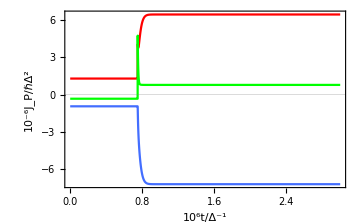
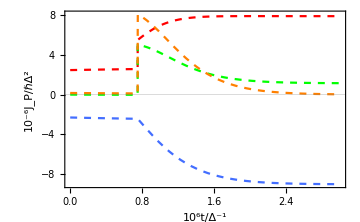
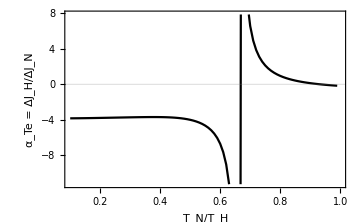
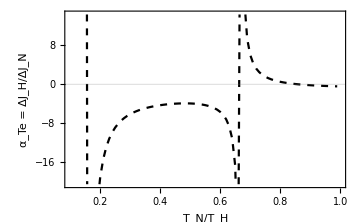
```mathematica
engdiv=-Graphics-;intbath=-Graphics-;
Legended[Show[engdiv,intbath,PlotRange->{-9,8}],LineLegend[{Red,Green,BlueC,Directive[Orange,Dashed]},{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5]}]]
engdiv=-Graphics-;intbath=-Graphics-;
Show[engdiv,intbath]
```

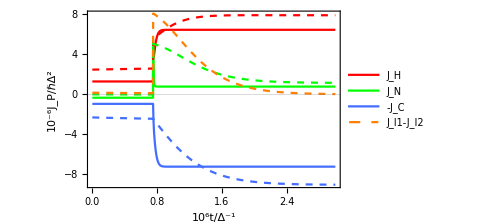

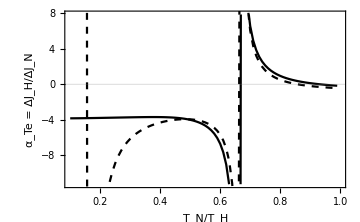

### Optically controlled

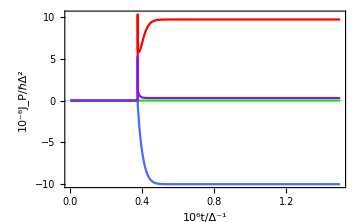
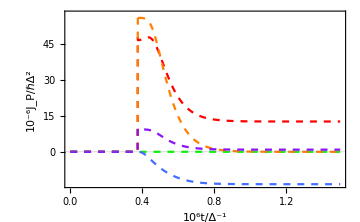
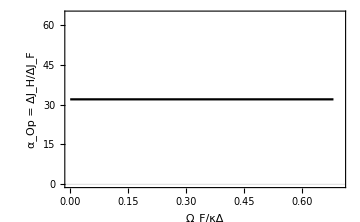
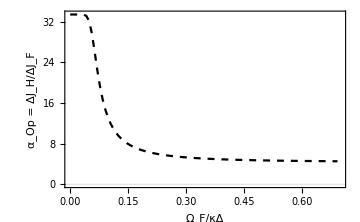
```mathematica
engdiv=-Graphics-;intbath=-Graphics-;
Legended[Show[engdiv,intbath,PlotRange->{-14,30}],LineLegend[{Red,Green,BlueC,PurpleC,Directive[Orange,Dashed]},{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5]}]]
engdiv=-Graphics-;intbath=-Graphics-;
Show[engdiv,intbath]
```

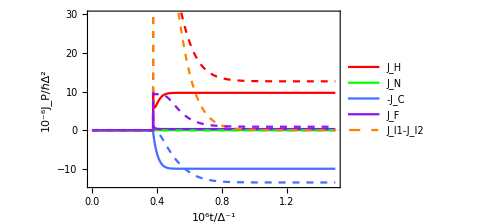

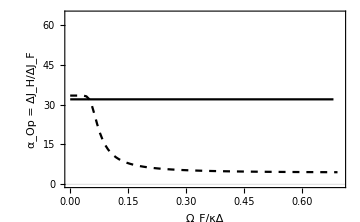

## ω_LM^S_1=0.3Δ, ω_MR^S_1=0.4Δ ω_LM^S_2=(1-0.4/6)Δ, ω_MR^S_2=(1+0.4/6)Δ ω_H=(0.4/3)Δ

### Temperature controlled

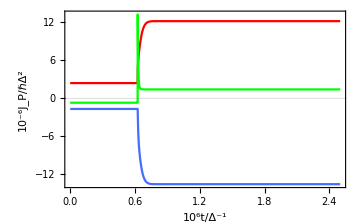
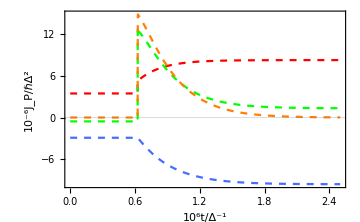
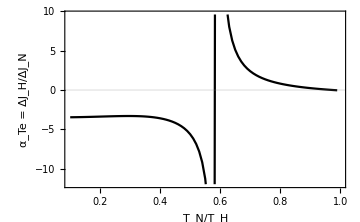
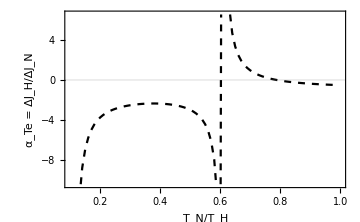
```mathematica
engdiv=-Graphics-;intbath=-Graphics-;
Legended[Show[engdiv,intbath,PlotRange->{-14,17}],LineLegend[{Red,Green,BlueC,Directive[Orange,Dashed]},{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5]}]]
engdiv=-Graphics-;intbath=-Graphics-;
Show[engdiv,intbath]
```

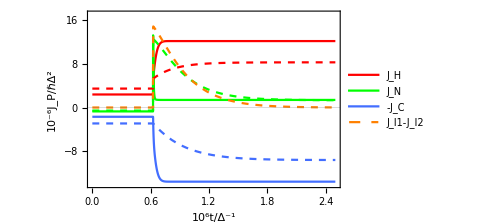

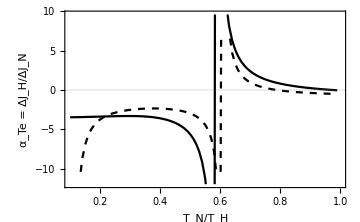

### Optically controlled

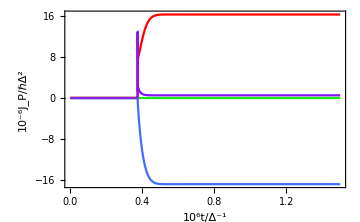
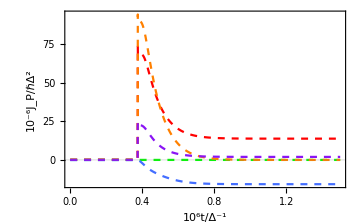
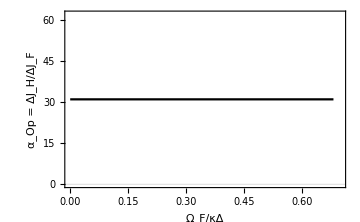
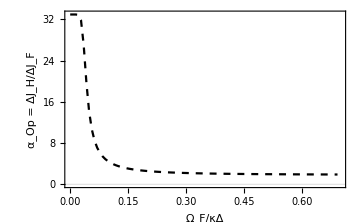
```mathematica
engdiv=-Graphics-;intbath=-Graphics-;
Legended[Show[engdiv,intbath,PlotRange->{-17,30}],LineLegend[{Red,Green,BlueC,PurpleC,Directive[Orange,Dashed]},{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5]}]]
engdiv=-Graphics-;intbath=-Graphics-;
Show[engdiv,intbath]
```

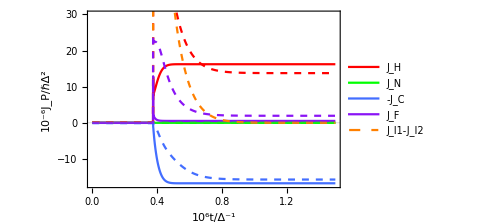

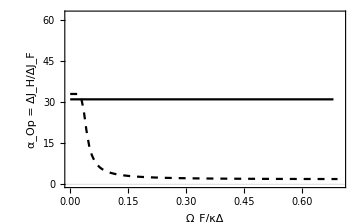

## Energy divider (3,2) analysis

## ω_LM^S_1=0.5Δ, ω_MR^S_1=0.6Δ ω_LM^S_2=0.8Δ, ω_MR^S_2=1.2Δ ω_H=0.2Δ

### Temperature controlled

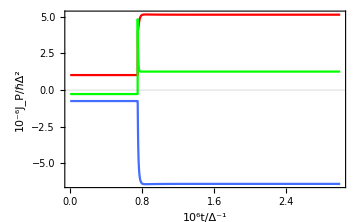
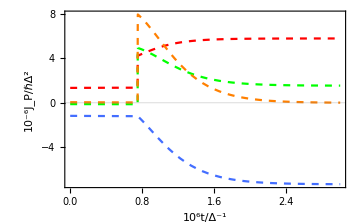
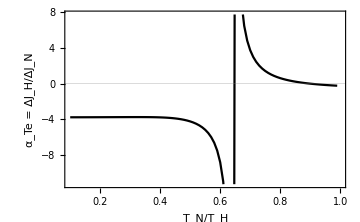
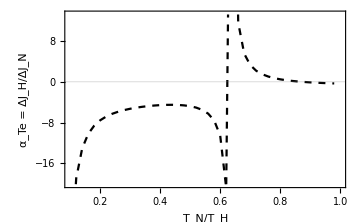
```mathematica
engdiv=-Graphics-;intbath=-Graphics-;
Legended[Show[engdiv,intbath,PlotRange->{-7,9}],LineLegend[{Red,Green,BlueC,Directive[Orange,Dashed]},{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5]}]]
engdiv=-Graphics-;intbath=-Graphics-;
Show[engdiv,intbath,PlotRange->{{0.1,1},{-10,6.5}}]
```

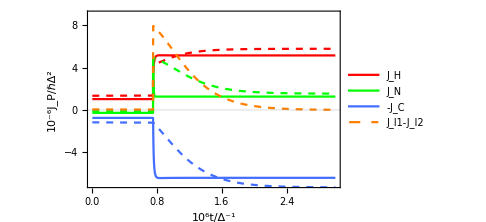

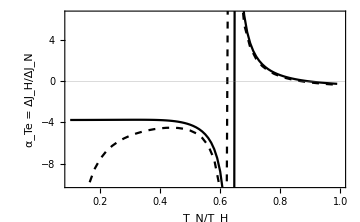

### Optically controlled

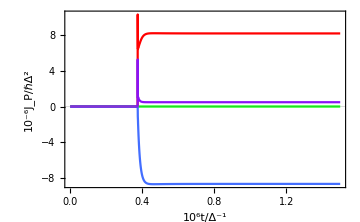
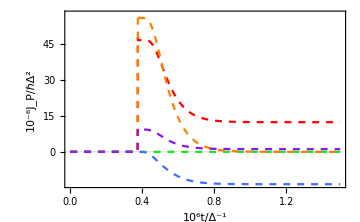
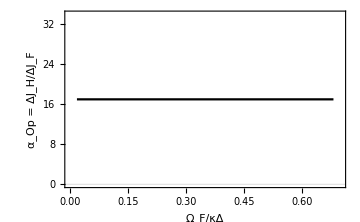
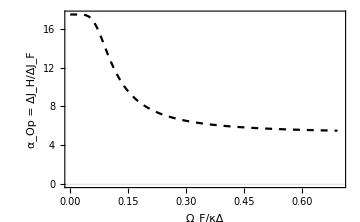
```mathematica
engdiv=-Graphics-;intbath=-Graphics-;
Legended[Show[engdiv,intbath,PlotRange->{-13,30}],LineLegend[{Red,Green,BlueC,PurpleC,Directive[Orange,Dashed]},{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5]}]]
engdiv=-Graphics-;intbath=-Graphics-;
Show[engdiv,intbath,PlotRange->{{0.0,0.7},{-1,22}}]
```

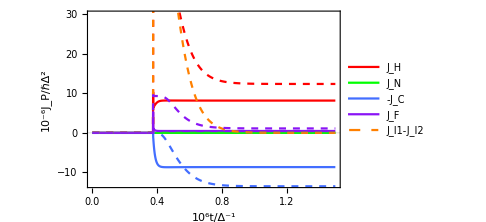

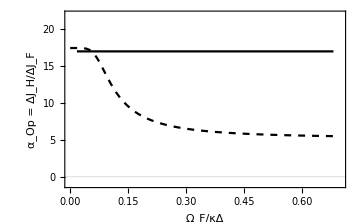

## ω_LM^S_1=0.3Δ, ω_MR^S_1=0.4Δ ω_LM^S_2=(1-2 0.4/6)Δ, ω_MR^S_2=(1+2 0.4/6)Δ ω_H=(0.4/3)Δ

### Temperature controlled

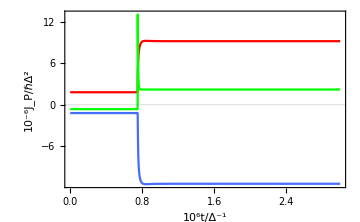
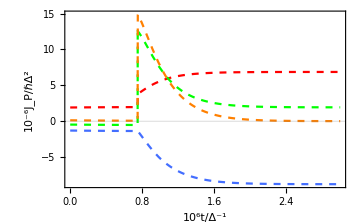
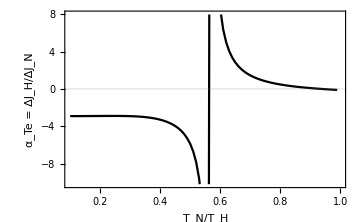
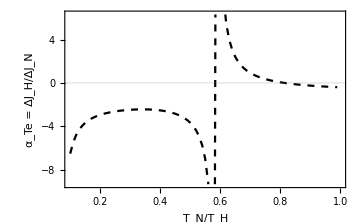
```mathematica
engdiv=-Graphics-;intbath=-Graphics-;
Legended[Show[engdiv,intbath,PlotRange->{-12,16}],LineLegend[{Red,Green,BlueC,Directive[Orange,Dashed]},{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5]}]]
engdiv=-Graphics-;intbath=-Graphics-;
Show[engdiv,intbath]
```

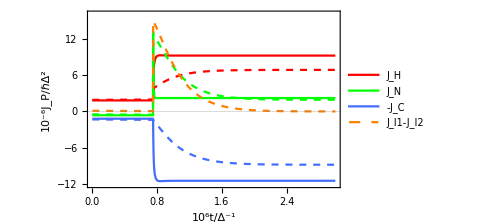

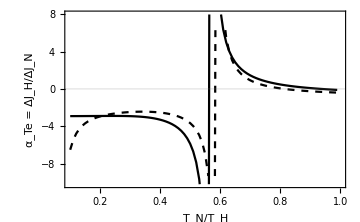

### Optically controlled

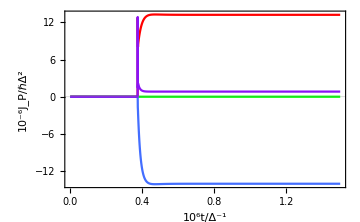
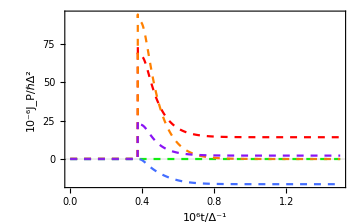
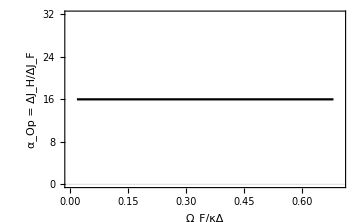
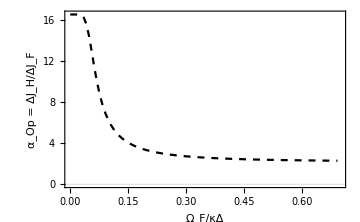
```mathematica
engdiv=-Graphics-;intbath=-Graphics-;
Legended[Show[engdiv,intbath,PlotRange->{-16,30}],LineLegend[{Red,Green,BlueC,PurpleC,Directive[Orange,Dashed]},{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5]}]]
engdiv=-Graphics-;intbath=-Graphics-;
Show[engdiv,intbath]
```